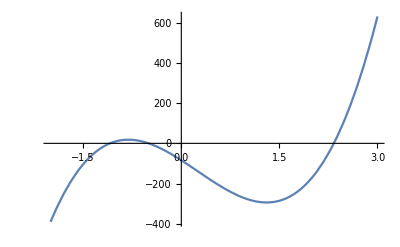

По графику видно, что уравнение имеет три действительных корня. Они расположены в интервалах (-2, -1), (-1,0),(2,3)

{{x→-12/11},{x→-1/2},{x→7/3}}

```mathematica
f[x_]:=66*x^3-49*x^2-209*x-84
Plot[f[x],{x,-2,3},AxesOrigin->{0,0}]
"По графику видно, что уравнение имеет три действительных корня. Они расположены в интервалах (-2, -1), (-1, 0),(2, 3)"
Solve[f[x]==0]
```

```mathematica
f[x_]:=66*x^3-49*x^2-209*x-84
"Вычислим корень с помощью метода половинного деления"
a=-2;
b=-1;
e=0.001;
Do[c=(a+b)/2.;
fc=f[c];
If[f[a]*fc<0,b=c, If[fc!=0,a=c]];
If[Abs[b-a]<e||fc==0,
Print["Решение x= ", c//N, " получено на ",n, " шаге."];
Break[]],
{n,1,100}]
```

Вычислим корень с помощью метода половинного деления

Решение x= -1.09082 получено на 10 шаге.

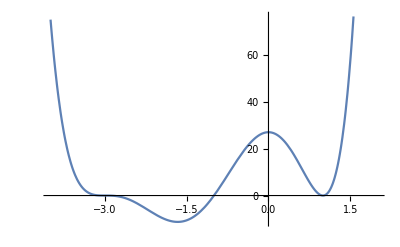

По графику видно, что уравнение имеет три действительных корня. Они расположены в интервалах ((-3.5, -2.5), (-1.5, -0.5),(0.5, 1.5)

```mathematica
f[x_]:=x^6+8*x^5+17*x^4-8*x^3-45*x^2+27
Plot[f[x],{x,-4,2},AxesOrigin->{0,0}]
"По графику видно, что уравнение имеет три действительных корня. Они расположены в интервалах ((-3.5, -2.5), (-1.5, -0.5),(0.5, 1.5)"
```

```mathematica
f[x_]:=x^6+8*x^5+17*x^4-8*x^3-45*x^2+27
"Найдем один из корней с помощью метода Ньютона"
a=-1.5;
b=-0.5;
e=0.001;
x1=a;

Do[x2=x1;
x1=(x1-f[x1]/f'[x1])//N;
If[Abs[x2-x1]<e,
Print["Решение x= ",x2//N," получено на n = ",n," шаге."];
Break[]],
{n,1,100}]
NSolve[f[x]==0]
```

Найдем один из корней с помощью метода Ньютона

Решение x= -0.999999 получено на n = 7 шаге.

{{x→-3.},{x→-3.},{x→-3.},{x→-1.},{x→1.},{x→1.}}

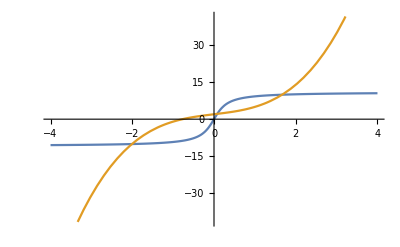

Уравнение имеет три действительных корня

Первый корень

{x→-2.00918}

Второй корень

{x→0.0796832}

Третий корень

{x→1.66568}

```mathematica
f[x_]:=7*ArcTan[4*x];
g[x_]:=x^3+2*x+2;
Plot[{f[x],g[x]},{x,-4,4},AxesOrigin->{0,0}]
"Уравнение имеет три действительных корня"
"Первый корень"
FindRoot[f[x]==g[x],{x,-2.5}]

"Второй корень"
FindRoot[f[x]==g[x],{x,0}]

"Третий корень"
FindRoot[f[x]==g[x],{x,1.5}]
```

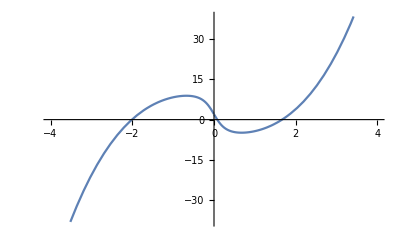

Вычислим корень с помощью метода хорд

{x→-2.00918}

{x→0.0796832}

{x→1.66568}

Решение x = 1.61302 получено на n = 3 шаге

```mathematica
f[x_]:=-7*ArcTan[4*x]+x^3+2*x+2
Plot[f[x],{x,-4,4},AxesOrigin->{0,0}]
"Вычислим корень с помощью метода хорд"
FindRoot[f[x],{x,-2.5}]
FindRoot[f[x],{x,0}]
FindRoot[f[x],{x,1}]

a=1;
b=3;
e=0.001;
x1=a;
x2=b;


Do[
xr=x1-(f[x1]*(x2-x1)/(f[x2]-f[x1]));
If[f''[x2]*f[x2]<0,
x1=xr];
If[f''[x1]*f[x1]<0,
x2=xr];
If[Abs[x2-x1]<e,
Print["Решение x = ",xr//N," получено на n = ",n," шаге"];
Break[]],
{n,1,100}]
```